```mathematica
p=RunProcess[{"python", "-c", "import comod;print(comod.sir.to_wolfram())"}]
```

<|ExitCode→0,StandardOutput→<|"system" -> {D[s[t], t] == -\[Beta] i[t] / n s[t],
D[i[t], t] == \[Beta] i[t] / n s[t] - \[Gamma] i[t],
D[r[t], t] == \[Gamma] i[t]},
"states" -> {s[t],i[t],r[t]},
"parameters" -> {\[Beta],\[Gamma]}|>
,StandardError→|>

```mathematica
data=ToExpression[p[["StandardOutput"]]]
```

<|system→{s'[t]==-(β i[t] s[t])/n,i'[t]==-γ i[t]+(β i[t] s[t])/n,r'[t]==γ i[t]},states→{s[t],i[t],r[t]},parameters→{β,γ}|>

```mathematica
sols=NDSolve[Join[data["system"],MapThread[Equal, {data["states"]/.t->0, {999,1,0}}]]/.{β->0.3, γ->0.1, n->1000},data["states"],{t,200}]
```

{{s[t]→InterpolatingFunction[…][t],i[t]→InterpolatingFunction[…][t],r[t]→InterpolatingFunction[…][t]}}

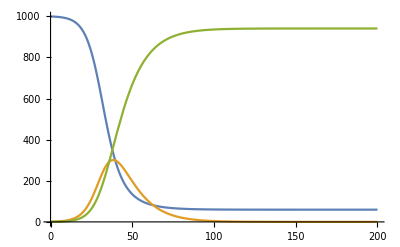

```mathematica
Plot[Evaluate[sols[[1,All,2]]],{t,0,200}, PlotRange->All]
```